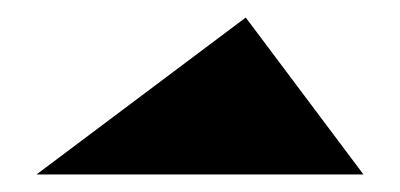

```mathematica
(* 01 *)
```

```mathematica
(* 02 *)
Graphics[SSSTriangle[3,4,5]]
```

-Graphics-

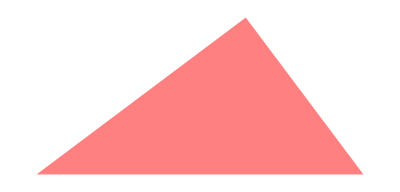

```mathematica
(* 03 *)
Graphics[{Pink,SSSTriangle[3,4,5]}]
```

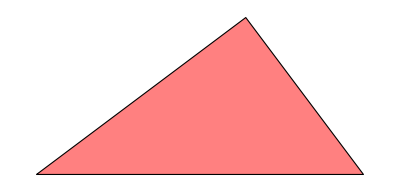

```mathematica
(* 04 *)
Graphics[{Pink,EdgeForm[{Black}],SSSTriangle[3,4,5]}]
```

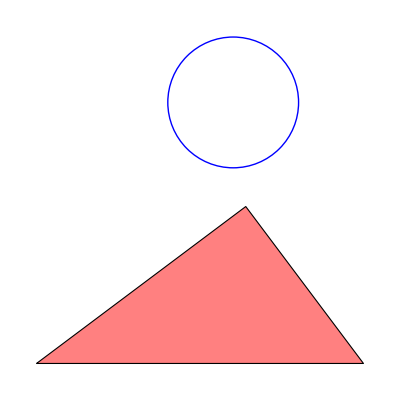

```mathematica
(* 05 *)
Graphics[{
Pink,EdgeForm[{Black}],SSSTriangle[3,4,5],
Blue,Circle[{3,4},1]
}]
```

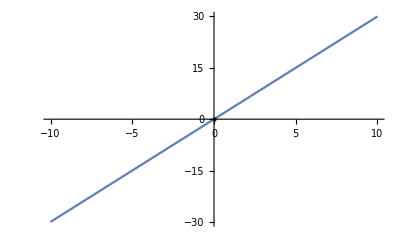

```mathematica
(* 06 *)
Plot[3x,{x,-10,10},Epilog->{PointSize[Large],Point[{0,0}]}]
```

```mathematica
(* 07 *)
Plot[3x,{x,-10,10},Epilog->{PointSize[Small],Point[{0,0}]}]
```

-Graphics-

```mathematica
(* 08 *)
Plot[3x,{x,-10,10},Epilog->{PointSize[Large],Point[{0,0}]}]
```

-Graphics-

```mathematica
(* 10 *)
```

```mathematica
Manipulate[
Plot[3x,{x,-10,10},Epilog->{PointSize[Large],Point[{t,3t}]}],
{t,-π,π}
]
```